1.68599 x-0.685987 x^2

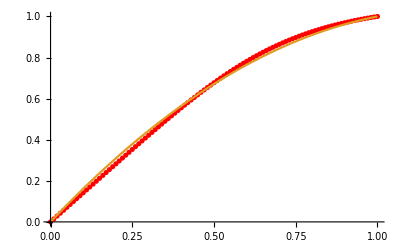

```mathematica
f[x_]:=(2/((2/(x^4)-2)/4+2))^(1/4)/;x>0
f[x_]:= 0/;x==0
data := Table[{x,f[x]},{x, 0,1,0.01}];
parabola = Normal[NonlinearModelFit[data, {a*x+b*x^2, a+b==1}, {a,b}, x]]
Show[ListPlot[data,PlotStyle->Red],Plot[{line,parabola},{x,0,1}]]
```

```mathematica
InverseFunction[a#+b#^2 &]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

(-a-√(a^2+4 b #1))/(2 b)&